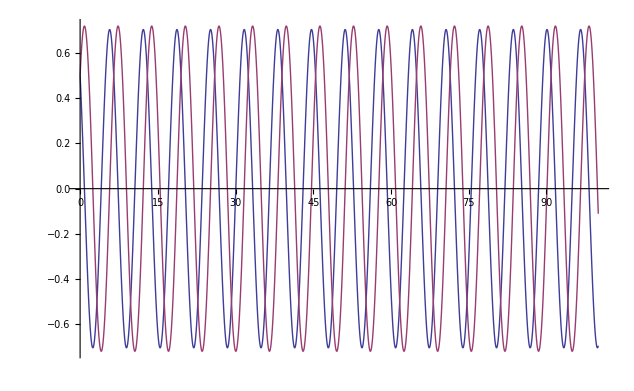

```mathematica
(*H ==(p[t]^2)/(2m l^2)+m g l(1 - Cos[θ[t]]); *)
val = {m ->1,l ->1,g ->1,p0 ->0.5,θ0->0.5};
sol =Flatten@NDSolve[{p'[t]== -m g l Sin[θ[t]],
θ'[t]== p[t]/(m l^2), p[0]==p0, θ[0]==θ0}/.val,{p[t],θ[t]},{t,0,100}];
Plot[{p[t]/.sol,θ[t]/.sol},{t,0,100},PlotRange ->Full]
```

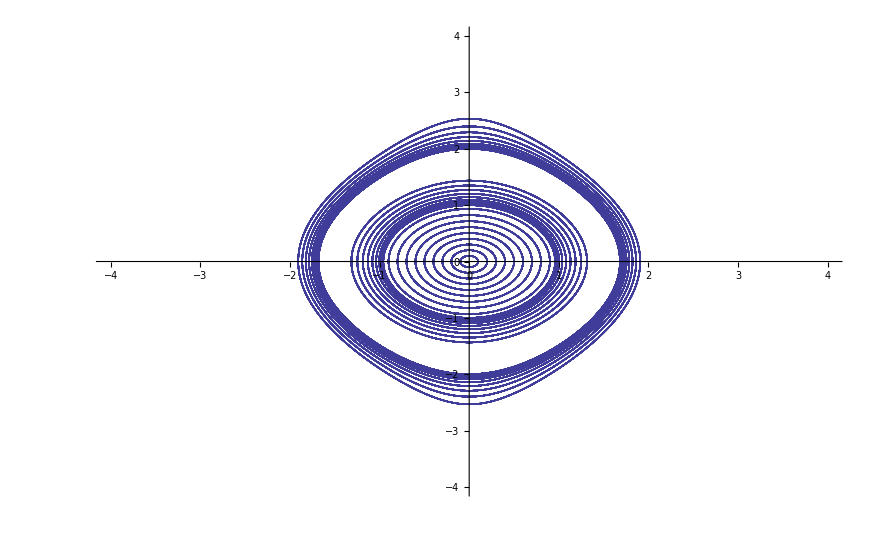

```mathematica
T=100;
sol =Table[
val={m->1,l->1,g->1,p0->a, θ0->b};
Flatten@NDSolve[{p'[t]== -m g l Sin[θ[t]],
θ'[t]== p[t]/(m l^2), p[0]==p0, θ[0]==θ0}/.val,{p[t],θ[t]},{t,0,100}]
,{a,0,0.9,0.1},{b,-2,2,1}]; (*these values are retwarded what does a negative angle even mean in this case?*)

ParametricPlot[{p[t], θ[t]}/.sol,{t,0,T},PlotRange->{{-4,4},{-4,4}}, AspectRatio->1/GoldenRatio]
```

```mathematica
T=100;
sol =Table[
val={m->1,l->1,g->1,p0->a, θ0->b};
Flatten@NDSolve[{p'[t]== -m g l Sin[θ[t]],
θ'[t]== p[t]/(m l^2), p[0]==p0, θ[0]==θ0}/.val,{p[t],θ[t]},{t,0,100}]
,{a,-1,1,0.1},{b,0,360,10}];

ParametricPlot[{p[t], θ[t]}/.sol,{t,0,T},PlotRange->{{-1,1},{0,360}}, AspectRatio->1/GoldenRatio]
```

$Aborted